```mathematica
Exit
```

```mathematica
p=0.31 2;
size=96p;
λ=0.810;
padRatio=2;
```

```mathematica
rotL[data_]:=RotateLeft[data, Floor@Dimensions[data][[#]]/2&/@Range[Length@Dimensions[data]]];
(* corner at orign to center at origin *)
rotR[data_]:=RotateRight[data, Floor@Dimensions[data][[#]]/2&/@Range[Length@Dimensions[data]]];
(* {x,y} means {x,y}/λ, {kx,ky} means {kx,ky}/k *)
FFT[f_] :=rotR[Fourier[f, FourierParameters->{1, -1}]];
iFFT[f_]:=InverseFourier[rotL[f], FourierParameters->{1, -1}];

centerRange[n_,d_]:=Table[(i-n/2-.5)*d,{i,n}];
```

```mathematica
k0=2π/λ
{nx,ny}={Floor[size/p],Floor[size/p]};
{lx,ly}={nx*p,ny*p};
{dx,dy}={p,p};
{dkx, dky}={(2π)/(p*nx),(2π)/(p*ny)};
{padx,pady}= {(padRatio-1)/2 nx,(padRatio-1)/2 ny};
{x,y}={centerRange[nx,dx],centerRange[ny,dy]};
Echo[{nx p,ny p},"Sample size in um: "];
Echo[{nx,ny},"Sample size in pixel: "];
```

7.75702

Sample size in um:   {59.52,59.52}

Sample size in pixel:   {96,96}

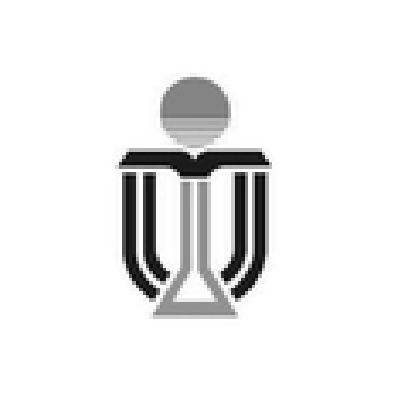

```mathematica
SetDirectory[NotebookDirectory[]];
img = Import["/home/stnav/Projects/jensen-lab-mathematica/hologram/hkust.png"];
target =img//ImageResize[#,{ny,nx}]&//ColorConvert[#, "Grayscale"]&//ImageData//#/Max[#]&//(1-#)&;
target//ArrayPlot
```

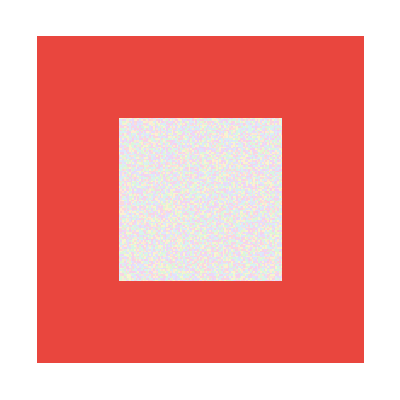

Thread::tdlen: Objects of unequal length in {{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},«86»} {«1»} cannot be combined.

Thread::tdlen: Objects of unequal length in {{-0.969797+0.243914 ⅈ,-0.91186+0.410502 ⅈ,0.988373+0.152049 ⅈ,0.57718-0.816617 ⅈ,-0.20397+0.978977 ⅈ,-0.786802-0.617206 ⅈ,0.996525-0.0832945 ⅈ,-0.843806+0.536648 ⅈ,-0.833475+0.552557 ⅈ,0.202207-0.979343 ⅈ,«182»},«9»,«182»} {{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},«9»,«86»} cannot be combined.

InverseFourier::fftl: Argument {{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},«86»} {«1»} is not a non-empty list or rectangular array of numeric quantities.

Thread::tdlen: Objects of unequal length in {{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},«86»} {«1»} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

InverseFourier::fftl: Argument {{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},«86»} {«1»} is not a non-empty list or rectangular array of numeric quantities.

$Aborted

Thread::tdlen: Objects of unequal length in {{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},«86»} {«1»} cannot be combined.

InverseFourier::fftl: Argument {{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«86»},«86»} {«1»} is not a non-empty list or rectangular array of numeric quantities.

```mathematica
gsLoop = 1;
source = ConstantArray[1,{ny,nx}]//ArrayPad[#, {pady, padx}]&;
loopA = source*Exp[ⅈ RandomReal[{0,2π},source//Dimensions]];
ComplexArrayPlot[loopA]
For[i = 0, i < gsLoop,i = i + 1,
loopB = Abs[source] * Exp[ⅈ*Arg[loopA]];
loopC = FFT[loopB];
loopD = Abs[target] * Exp[ⅈ*Arg[loopC]];
loopA = iFFT[loopD];
]
Enear = source * Exp[ⅈ* Arg[loopA]];
ComplexArrayPlot[Enear];
```